Set::write: Tag Integer in 20[2] is Protected.

Set::write: Tag Integer in 20[3] is Protected.

Set::write: Tag Integer in 20[4] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Integer in 80[1] is Protected.

Set::write: Tag Integer in 80[2] is Protected.

Set::write: Tag Integer in 80[3] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Integer in 20[1] is Protected.

Set::write: Tag Integer in 20[2] is Protected.

Set::write: Tag Integer in 20[3] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Integer in 20[0] is Protected.

Set::write: Tag Integer in 20[1] is Protected.

Set::write: Tag Integer in 20[2] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag Integer in 80[0] is Protected.

Set::write: Tag Integer in 80[1] is Protected.

Set::write: Tag Integer in 80[2] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

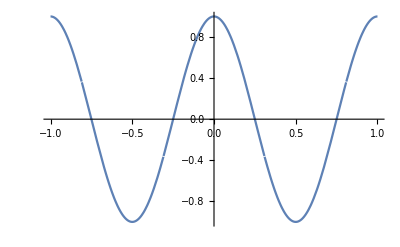

-Graphics-

```mathematica
n=5;
(*дефинираме функцията,която ще се интерполира*)
f[t_]:=Cos[2*Pi*t];
(*Инициализация на възлите хk k=0,..n*)
Do[x[i]=k/n,{k, 0, n}];
(*разстоянието между всеки два съседни възела->Δ[k]*)
(*методът на прогонката*)
(*1. Изчисляваме коефициентите пред неизвестните s0,s1,...,sn*)
delta = 1/n;
aa = 1/delta;
bb = 4/delta;
cc = 1/delta
(*Резултатът от дясната страна на равенството*)
Do[d[k]=3*((f[x[k]]-f[x[k-1]])/delta^2+(f[x[k+1]]-f[x[k]])/delta^2),{k,1,n-1}];
(*2. Намираме α и β*)
alpha[1]=-cc/bb;
beta[1]=d[1]/bb;
(*и изразяваме α[k] и β[k]*)
Do[alpha[k]=-cc/(aa*alpha[k-1]+bb),{k,2,n-2}];
Do[beta[k]=(d[k]-aa*beta[k-1])/(aa*alpha[k-1]+bb),{k,2,n-1}];
(*намираме s[0] и s[n]*)
s[0]=0;
s[n]=0;
s[n-1]=beta[n-1];
Do[s[k]=alpha[k]*s[k+1]+beta[k],{k,n-1,1,-1}];
(*общ вид на полиномите интерполиращи f(t) във всеки интервал на[-1,1],определен от два последователни възела*)
Do[a[k]=(f[x[k+1]]-f[x[k]])/h[k]^2-s[k]/h[k],{k,0,n-1}];
Do[b[k]=s[k+1]/h[k]^2+s[k]/h[k]^2+2*(f[x[k]]-f[x[k+1]])/h[k]^3,{k,0,n-1}];
Do[P[k,t_]=f[x[k]]+s[k]*(t-x[k])+a[k] (t-x[k])^2+b[k]*(t-x[k])^2*(t-x[k+1]),{k,0,n-1}];
(*построяваме кубичния сплайн за f(t)*)
S[t_]:=Sum[If[t≥x[k]&&t≤x[k+1],P[k,t],0],{k,0,n-1}];
(*графиките на функцията и сплайн функцията*)
Plot[{f[t],S[t]},{t,-1,1},PlotRange->All]
Plot[f[t]-S[t],{t,-1,1},PlotRange->All]
```